## Walter, Differential Equations. Problem Set, page 23.

### (b) y'=(y+1)/(x+2)+ⅇ^((y+1)/(x+2))

Solution: y=(-x-2) log(c-log(Abs[x+2]))-1;     Abs[x+2]<exp(c). All solutions pass through (-2,-1) and have derivatives that approach negative infinity at that point.

```mathematica
Solve[0==-2Log[c-Log[2]]-1,c]
```

{{c→1/(√ⅇ)+Log[2]}}

```mathematica
fb1[x_,y_]:=(y+1)/(x+2)
```

```mathematica
fb2[x_,y_]:=fb1[x,y]+Exp[fb1[x,y]]
```

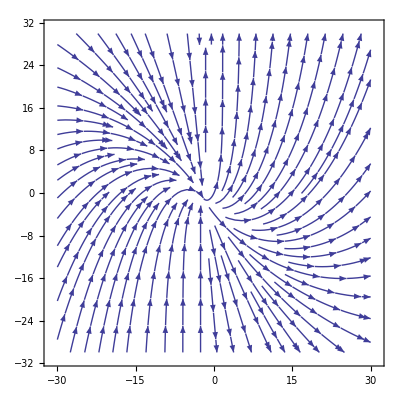

```mathematica
streamplot=StreamPlot[{1,fb2[x,y]},{x,-30,30},{y,-30,30}]
```

Let u=(y+1)/(x+2). So y'=(x+2) u'+u = exp(u)+u. So exp(-u) u'=1/(x+2). So exp(-u) ⅆu=ⅆx/(x+2). So -exp(-u)=log(Abs[x+2])+c.
So u=-log(c-log(Abs[x+2])) so y=-(x+2) log(c-log(Abs[x+2]))-1

```mathematica
fb4[x_]:=-(x+2)Log[c-Log[x+2]]-1
```

```mathematica
fb4[x]//TraditionalForm
```

(-x-2) log(c-log(x+2))-1

```mathematica
FullSimplify[fb4'[x]]//TraditionalForm
```

1/(c-log(x+2))-log(c-log(x+2))

```mathematica
FullSimplify[fb2[x,fb4[x]]]//TraditionalForm
```

1/(c-log(x+2))-log(c-log(x+2))

```mathematica
fb5[x_]:=-(x+2)Log[c-Log[Abs[x+2]]]-1
```

```mathematica
fb5[x]//TraditionalForm
```

(-x-2) log(c-log(Abs[x+2]))-1

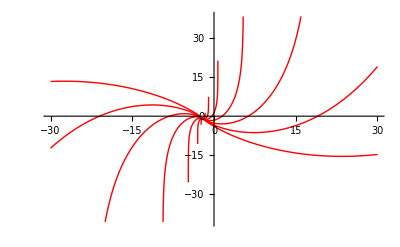

```mathematica
plot=Plot[Table[fb5[x]/.c->d,{d,-5,5}],{x,-30,30},PlotStyle->{Red,Thick}]
```

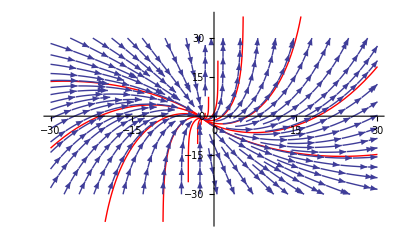

```mathematica
Show[plot,streamplot]
```

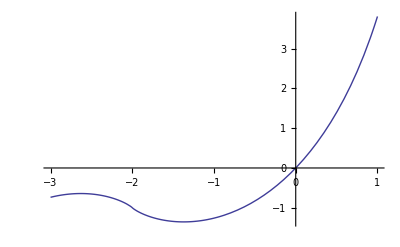

```mathematica
Plot[fb5[x]/.c->1/(√ⅇ)+Log[2],{x,-3,1}]
```

```mathematica
Limit[fb5[x],x->-2]
```

-1

```mathematica
Limit[fb5'[x],x->-2]
```

-∞

### (d) y'=(x+2y+1)/(2 x+y+2)

```mathematica
fd1[x_,y_]:=(x+2y+1)/(2x+y+2)
```

```mathematica
fd1[x,y]//TraditionalForm
```

(x+2 y+1)/(2 x+y+2)

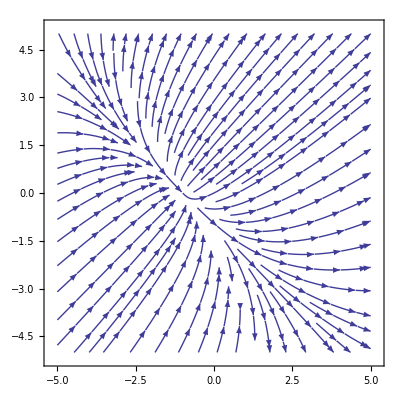

```mathematica
StreamPlot[{1,fd1[x,y]},{x,-5,5},{y,-5,5}]
```

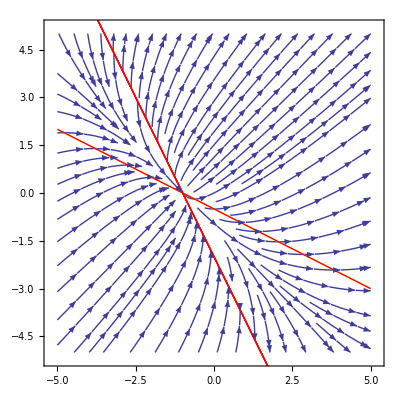

```mathematica
Show[{%,Plot[-2x-2,{x,-5,5}, PlotStyle->Red],Plot[-(1/2)x-(1/2),{x,-5,5}, PlotStyle->Red]}]
```

Let u=x-1

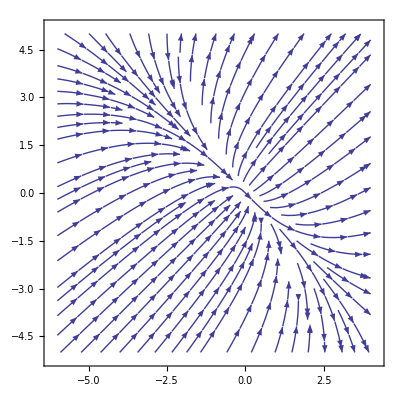

```mathematica
fd2[u_,y_]:= (u+2y)/(2u+y)
StreamPlot[{1,fd2[u,y]},{u,-6,4},{y,-5,5},Axes->True]
```